```mathematica
(*QuEST VQD Setup*)
Import["https://qtechtheory.org/questlink.m"]
CreateDownloadedQuESTEnv[];
Get["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\vqd CG V3 Parallel.wl"]
```

URLDownload::invhttp: Failed writing body (0 != 15452).

```mathematica
data=Import["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\SU4Gates9Qubits.csv"];
```

```mathematica
distloc[q1_, q2_] := 
			Norm[RydDev[AtomLocations][q1] - RydDev[AtomLocations][q2], 2] RydDev[UnitLattice];

blockadecheck[q_List] := 
			And @@ ((distloc @@ # <= (RydDev[BlockadeRadius]+$MachineEpsilon))& /@ Subsets[Flatten[q], {2}]);
```

```mathematica
(*VQD Initialisation*)locations=Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}];
Options[RydbergHub]={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> locations
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 1.49*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 4*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0, 01->0|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> 1
,
(* blockade radius of each atom *)
BlockadeRadius -> 10
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 0
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.003(*0.007*)
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 100
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 300
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 100
,
DurMeas -> 2*10^4
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
RydDev=RydbergHub[];
PlotAtoms[RydbergHub[]]
```

-Graphics3D-

```mathematica
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
NRandQbits[NQ_,i_]:=If[i==0,Range[0,NQ-1],RandomSample[Range[0,NQ-1],NQ]]
CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];
```

```mathematica
SU4GateARPMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]
```

```mathematica
NQ=5
RQs={0,1,2,3,4}
ARPCZdur=1
(*Parallelised SU4 Gate layer generators*)
SU4GateARPParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

SU4GatePIParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZPIPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

MoveTime=300
QVLayerARPParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GateARPParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SpareARP, RQs[[-1]]],Subscript[Wait, 0][MoveTime]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1]
QVLayerPIParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GatePIParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SparePI, RQs[[-1]]],Subscript[Wait, 0][MoveTime]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1]
```

5

{0,1,2,3,4}

1

300

```mathematica
QVLayerARPMove[DataSet_,NQ_,RQs_,i_]:=Join[Table[SU4GateARPMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}],2];
```

```mathematica
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]
(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Which[StringContainsQ[ConnectivityRule,"ARPA2A"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPA2A[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPSWAP"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPSWAP[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIA2A"],
Table[RQS=NRandQbits[NQ,i];QVLayerPIA2A[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PISWAP"],
Table[RQS=NRandQbits[NQ,i];QVLayerPISWAP[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerPIMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIParMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerPIParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPParMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}]
]
```

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
(*Perfect renormalisation on a given circuit, unsure if this is best or if taking an average across the NCirc is a more "accurate" scheme*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Circ1=Flatten[QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule],1];
Initialisation={InitCirc[Reg,MaxNQ]};
InitCircuit=Join[Initialisation,Circ1];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
PNoLoss=Total[PoutcomesNoisy];
PoutcomesNoisyRen=PoutcomesNoisy/PNoLoss;
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
HeavyOutputsRen=CheckHeavyOutputProb[PoutcomesNoisyRen,PoutcomesModel];
{Total[HeavyOutputs],Total[HeavyOutputsRen],1-PNoLoss},{Rep,0,NReps-1,1}]


(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_,ConnectivityRule_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
DestroyAllQuregs[];
MHOP=Mean[HOP[[All,1]]];
MHOPRen=Mean[HOP[[All,2]]];
MPLoss=Mean[HOP[[All,3]]];
σPLoss=StandardDeviation[HOP[[All,3]]]/Sqrt[NReps-1];
σ=StandardDeviation[HOP[[All,1]]]/Sqrt[NReps-1];
σRen=StandardDeviation[HOP[[All,2]]]/Sqrt[NReps-1];
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
If[ Re[(MHOPRen-2σRen)]>2/3,VQRen=2^NQ,VQRen=0];
Print[{"Layer",NQ,VQ,VQRen}];
{{NQ,MHOP,2σ},{NQ,MHOPRen,2σRen},{NQ,MPLoss,σPLoss}}
,{NQ,2,MaxNQ,1}];
```

```mathematica
QVCalc[data,9,2,"PIParMove"]
```

{Layer,2,0,0}

{Layer,3,8,8}

{Layer,4,0,0}

{Layer,5,32,32}

{Layer,6,64,64}

{Layer,7,128,128}

{Layer,8,256,256}

{Layer,9,512,512}

{{{2,0.671346,0.284699},{2,0.693182,0.293938},{2,0.0315027,0.0000151381}},{{3,0.826416,0.139787},{3,0.856599,0.14582},{3,0.0352137,0.000524363}},{{4,0.75382,0.216757},{4,0.791895,0.228059},{4,0.0480652,0.000215059}},{{5,0.809352,0.000890897},{5,0.855619,0.00192775},{5,0.0540744,0.000544992}},{{6,0.776792,0.0503712},{6,0.839265,0.0562116},{6,0.0744219,0.000987223}},{{7,0.774672,0.00246059},{7,0.844429,0.00432674},{7,0.0826072,0.000893339}},{{8,0.738494,0.0038956},{8,0.831797,0.00344986},{8,0.11217,0.000500548}},{{9,0.731493,0.0181886},{9,0.832864,0.0206464},{9,0.121715,0.0000331225}}}

```mathematica
CalcCircuitMatrix[ExtractCircuit[GetCircuitSchedule[{Subscript[CZPIPar, 0,1]},RydDev,ReplaceAliases->True]]]
```

InsertCircuitNoise::error: Encountered gate CZPIPar_(0,1) which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

CalcCircuitMatrix::error: Circuit contained an unrecognised or unsupported gate: $Failed

$Failed

```mathematica
ParallelLayer=QVLayerPIParMove[{data[[200]],data[[1000]]},5,{0,1,2,3,4},0]
TestRho=CreateDensityQureg[9];
InitZeroState[TestRho];
NoisyCirc=InsertCircuitNoise[ParallelLayer,RydDev,ReplaceAliases->True]
ParCircSched=GetCircuitSchedule[ParallelLayer,RydDev,ReplaceAliases->True]
DrawCircuit[%]
ApplyCircuit[TestRho,ExtractCircuit[ParCircSched]]
```

QVLayerPIParMove[{{['Rx', [0.0], [1.7900363404195456]],['Ry', [0.0], [1.4670430226234354]],['Rx', [0.0], [-2.484570045260593]],['Rx', [1.0], [1.8861283750123876]],['Ry', [1.0], [2.5569424815452573]],['Rx', [1.0], [2.509739273829867]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [2.2117766315814684]],['Ry', [0.0], [3.141592653589793]],['Rx', [1.0], [0.37769195058327476]],['Ry', [1.0], [-1.5707963267948966]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [1.2196690476758798]],['Ry', [0.0], [1.5707963267948966]],['Rx', [0.0], [-1.5707963267948966]],['Rx', [1.0], [1.5707963267948966]],['Ry', [1.0], [1.5707963267948966]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [1.672338589319752]],['Ry', [0.0], [0.7530375632248356]],['Rx', [0.0], [-2.653585823624521]],['Rx', [1.0], [0.6372743114520656]],['Ry', [1.0], [2.3118928078424674]],['Rx', [1.0], [-2.1244988388046213]]},{['Rx', [0.0], [-1.800315039289523]],['Ry', [0.0], [1.2718519181503427]],['Rx', [0.0], [-1.008282709541314]],['Rx', [1.0], [2.3115020985994335]],['Ry', [1.0], [1.5727767539363633]],['Rx', [1.0], [-1.2363677858856938]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [2.1838751507695022]],['Ry', [0.0], [3.141592653589793]],['Rx', [1.0], [0.08047640854824678]],['Ry', [1.0], [-1.5707963267948968]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [1.8392828206538194]],['Ry', [0.0], [1.5707963267948963]],['Rx', [0.0], [-1.5707963267948966]],['Rx', [1.0], [1.5707963267948966]],['Ry', [1.0], [1.5707963267948966]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [-1.9660531239738477]],['Ry', [0.0], [1.7008475322590162]],['Rx', [0.0], [-2.552028929075849]],['Rx', [1.0], [-2.488052553022853]],['Ry', [1.0], [2.485809942797934]],['Rx', [1.0], [2.1499700971619315]]}},5,{0,1,2,3,4},0]

InsertCircuitNoise::error: Invalid arguments. See ?InsertCircuitNoise

$Failed

GetCircuitSchedule::error: Invalid arguments. See ?GetCircuitSchedule

$Failed

DrawCircuit::error: Invalid arguments. See ?DrawCircuit

$Failed

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

ApplyCircuit::error: Invalid arguments. See ?ApplyCircuit

$Failed

{{Rx_0[1.79004],Rx_1[1.88613],Rx_2[-1.80032],Rx_3[2.3115]},{Ry_0[1.46704],Ry_1[2.55694],Ry_2[1.27185],Ry_3[1.57278]},{Rx_0[-2.48457],Rx_1[2.50974],Rx_2[-1.00828],Rx_3[-1.23637]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[2.21178],Rx_1[0.377692],Rx_2[2.18388],Rx_3[0.0804764]},{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[1.21967],Rx_1[1.5708],Rx_2[1.83928],Rx_3[1.5708]},{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]},{Rx_0[-1.5708],Rx_2[-1.5708]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[1.67234],Rx_1[0.637274],Rx_2[-1.96605],Rx_3[-2.48805]},{Ry_0[0.753038],Ry_1[2.31189],Ry_2[1.70085],Ry_3[2.48581]},{Rx_0[-2.65359],Rx_1[-2.1245],Rx_2[-2.55203],Rx_3[2.14997]}}

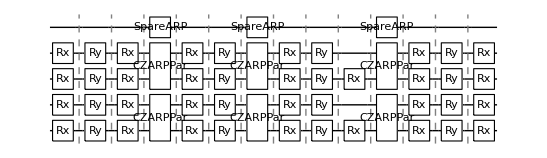

7

```mathematica
ParallelLayerOld={{Subscript[Rx, 0][1.7900363404195456],Subscript[Rx, 1][1.8861283750123876],Subscript[Rx, 2][-1.800315039289523],Subscript[Rx, 3][2.3115020985994335]},{Subscript[Ry, 0][1.4670430226234354],Subscript[Ry, 1][2.5569424815452573],Subscript[Ry, 2][1.2718519181503427],Subscript[Ry, 3][1.5727767539363633]},{Subscript[Rx, 0][-2.484570045260593],Subscript[Rx, 1][2.509739273829867],Subscript[Rx, 2][-1.008282709541314],Subscript[Rx, 3][-1.2363677858856938]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][2.2117766315814684],Subscript[Rx, 1][0.37769195058327476],Subscript[Rx, 2][2.1838751507695022],Subscript[Rx, 3][0.08047640854824678]},{Subscript[Ry, 0][3.141592653589793],Subscript[Ry, 1][-1.5707963267948966],Subscript[Ry, 2][3.141592653589793],Subscript[Ry, 3][-1.5707963267948968]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][1.2196690476758798],Subscript[Rx, 1][1.5707963267948966],Subscript[Rx, 2][1.8392828206538194],Subscript[Rx, 3][1.5707963267948966]},{Subscript[Ry, 0][1.5707963267948966],Subscript[Ry, 1][1.5707963267948966],Subscript[Ry, 2][1.5707963267948963],Subscript[Ry, 3][1.5707963267948966]},{Subscript[Rx, 0][-1.5707963267948966],Subscript[Rx, 2][-1.5707963267948966]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][1.672338589319752],Subscript[Rx, 1][0.6372743114520656],Subscript[Rx, 2][-1.9660531239738477],Subscript[Rx, 3][-2.488052553022853]},{Subscript[Ry, 0][0.7530375632248356],Subscript[Ry, 1][2.3118928078424674],Subscript[Ry, 2][1.7008475322590162],Subscript[Ry, 3][2.485809942797934]},{Subscript[Rx, 0][-2.653585823624521],Subscript[Rx, 1][-2.1244988388046213],Subscript[Rx, 2][-2.552028929075849],Subscript[Rx, 3][2.1499700971619315]}}
DrawCircuit[%]
```

```mathematica
{{0,{Subscript[Rx, 0][1.7900363404195456],Subscript[Rx, 1][1.8861283750123876],Subscript[Rx, 2][-1.800315039289523],Subscript[Rx, 3][2.3115020985994335]}},{2.3115020985994335,{Subscript[Ry, 0][1.4670430226234354],Subscript[Ry, 1][2.5569424815452573],Subscript[Ry, 2][1.2718519181503427],Subscript[Ry, 3][1.5727767539363633]}},{4.868444580144691,{Subscript[Rx, 0][-2.484570045260593],Subscript[Rx, 1][2.509739273829867],Subscript[Rx, 2][-1.008282709541314],Subscript[Rx, 3][-1.2363677858856938]}},{7.378183853974558,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{7.378183853974558,{Subscript[Rx, 0][2.2117766315814684],Subscript[Rx, 1][0.37769195058327476],Subscript[Rx, 2][2.1838751507695022],Subscript[Rx, 3][0.08047640854824678]}},{9.589960485556027,{Subscript[Ry, 0][3.141592653589793],Subscript[Ry, 1][-1.5707963267948966],Subscript[Ry, 2][3.141592653589793],Subscript[Ry, 3][-1.5707963267948968]}},{12.73155313914582,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{12.73155313914582,{Subscript[Rx, 0][1.2196690476758798],Subscript[Rx, 1][1.5707963267948966],Subscript[Rx, 2][1.8392828206538194],Subscript[Rx, 3][1.5707963267948966]}},{14.57083595979964,{Subscript[Ry, 0][1.5707963267948966],Subscript[Ry, 1][1.5707963267948966],Subscript[Ry, 2][1.5707963267948963],Subscript[Ry, 3][1.5707963267948966]}},{16.141632286594536,{Subscript[Rx, 0][-1.5707963267948966],Subscript[Rx, 2][-1.5707963267948966]}},{17.712428613389434,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{17.712428613389434,{Subscript[Rx, 0][1.672338589319752],Subscript[Rx, 1][0.6372743114520656],Subscript[Rx, 2][-1.9660531239738477],Subscript[Rx, 3][-2.488052553022853]}},{20.20048116641229,{Subscript[Ry, 0][0.7530375632248356],Subscript[Ry, 1][2.3118928078424674],Subscript[Ry, 2][1.7008475322590162],Subscript[Ry, 3][2.485809942797934]}},{22.686291109210224,{Subscript[Rx, 0][-2.653585823624521],Subscript[Rx, 1][-2.1244988388046213],Subscript[Rx, 2][-2.552028929075849],Subscript[Rx, 3][2.1499700971619315]}},{25.339876932834745,{}}}
```

```mathematica
InsertCircuitNoise[{Subscript[SpareARP, 0]},RydDev,ReplaceAliases->True]
```

{{0,{Deph_0[4.36241×10^-7]},{Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}},{0,{},{}}}

5

{0,1,2,3,4}

1

General::munfl: Exp[-671141.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{Rx_0[-1.39898],Rx_1[2.35008],Rx_2[-0.261282],Rx_3[-1.28709]},{Ry_0[1.62867],Ry_1[0.941758],Ry_2[0.792034],Ry_3[0.936994]},{Rx_0[1.45827],Rx_1[-0.467045],Rx_2[2.46382],Rx_3[-2.28206]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.96106],Rx_1[0.231888],Rx_2[2.25239],Rx_3[0.0229398]},{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.81862],Rx_1[1.5708],Rx_2[1.33254],Rx_3[1.5708]},{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]},{Rx_0[-1.5708],Rx_2[-1.5708]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.13586],Rx_1[-1.30951],Rx_2[-1.54958],Rx_3[3.07285]},{Ry_0[1.30701],Ry_1[1.57267],Ry_2[2.11492],Ry_3[2.72632]},{Rx_0[-0.417784],Rx_1[2.88766],Rx_2[1.0991],Rx_3[-1.01639]}}

{{0,{Rx_0[-1.39898],Rx_1[2.35008],Rx_2[-0.261282],Rx_3[-1.28709]}},{2.35008,{Ry_0[1.62867],Ry_1[0.941758],Ry_2[0.792034],Ry_3[0.936994]}},{3.97875,{Rx_0[1.45827],Rx_1[-0.467045],Rx_2[2.46382],Rx_3[-2.28206]}},{6.44257,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{7.74257,{Rx_0[1.96106],Rx_1[0.231888],Rx_2[2.25239],Rx_3[0.0229398]}},{9.99496,{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]}},{13.1366,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{14.4366,{Rx_0[1.81862],Rx_1[1.5708],Rx_2[1.33254],Rx_3[1.5708]}},{16.2552,{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]}},{17.826,{Rx_0[-1.5708],Rx_2[-1.5708]}},{19.3968,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{20.6968,{Rx_0[1.13586],Rx_1[-1.30951],Rx_2[-1.54958],Rx_3[3.07285]}},{23.7696,{Ry_0[1.30701],Ry_1[1.57267],Ry_2[2.11492],Ry_3[2.72632]}},{26.4959,{Rx_0[-0.417784],Rx_1[2.88766],Rx_2[1.0991],Rx_3[-1.01639]}},{29.3836,{}}}

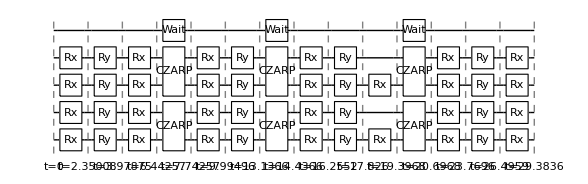

RydbergHub[T2]

```mathematica
?InsertCircuitNoise
```

```mathematica
QVLayerARPMove[DataSet_,NQ_,RQs_,i_]:=Join[Table[SU4GateARPMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}],2];
```

```mathematica
SU4GateARPMove[data[[1]],0,1]
SU4GateARPMove[data[[4]],0,1]
```

{{Rx_0[-1.39898],Ry_0[1.62867],Rx_0[1.45827],Rx_1[2.35008],Ry_1[0.941758],Rx_1[-0.467045]},{CZARP_(0,1)},{Rx_0[1.96106],Ry_0[3.14159],Rx_1[0.231888],Ry_1[-1.5708]},{CZARP_(0,1)},{Rx_0[1.81862],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708]},{CZARP_(0,1)},{Rx_0[1.13586],Ry_0[1.30701],Rx_0[-0.417784],Rx_1[-1.30951],Ry_1[1.57267],Rx_1[2.88766]}}

```mathematica
?Join
```

```mathematica
?GetCircuitSchedule
```

```mathematica
?Wait
```

```mathematica
InsertCircuitNoise[CircRydbergHub[{Subscript[Wait, 0][1000]},RydDev,Parallel->True],RydDev]
```

{{0,{Deph_0[0.000335458]},{Deph_0[0.],Deph_1[0.000335458],Deph_2[0.000335458],Deph_3[0.000335458],Deph_4[0.000335458],Deph_5[0.000335458],Deph_6[0.000335458],Deph_7[0.000335458],Deph_8[0.000335458]}},{1000,{},{}}}

{{0,{Rx_0[π],Deph_0[1.67785×10^-7],Rx_1[π],Deph_1[1.67785×10^-7]},{Deph_0[0.],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}},{π,{},{Deph_0[-∞],Deph_1[-∞],Deph_2[-∞],Deph_3[-∞],Deph_4[-∞],Deph_5[-∞],Deph_6[-∞],Deph_7[-∞],Deph_8[-∞]}}}

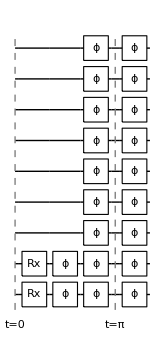

7

7

{Rx_0[π],Deph_0[1.67785×10^-7],Rx_1[π],Deph_1[1.67785×10^-7],Deph_0[0.],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Deph_0[-∞],Deph_1[-∞],Deph_2[-∞],Deph_3[-∞],Deph_4[-∞],Deph_5[-∞],Deph_6[-∞],Deph_7[-∞],Deph_8[-∞]}

ApplyCircuit::error: Circuit contains non-numerical or non-real parameters!

$Failed

```mathematica
Tes=InsertCircuitNoise[GetCircuitSchedule[CircRydbergHub[{Subscript[Rx, 0][Pi],Subscript[Rx, 1][Pi]},RydDev,Parallel->True],RydDev],RydDev]
DrawCircuit[%]
Te=CreateDensityQureg[9]
InitZeroState[Te]
ExtractCircuit[Tes]
ApplyCircuit[Te,ExtractCircuit[Tes]]
```

```mathematica
?GetCircuitSchedule
```

```mathematica
?ApplyCircuit
```

```mathematica
?QuEST`Gate`*
```

```mathematica
CalcCircuitMatrix[{Subscript[Id, 0]}]
```

{{1,0},{0,1}}